# Finding fixed points and the best responses graph of 2p2a games.

```mathematica
(*Check if player 2 uses the best strategy against player 1 and vice versa.*)
result[i_]:=
Module[{input = i},
(*Make assumptions on the Q-values and the game, based on the strategy.*)
assumptions = {
               If[input[[1]]==0, Q1000>Q1001, Q1000<Q1001],
               If[input[[2]]==0, Q1010>Q1011, Q1010<Q1011],
               If[input[[3]]==0, Q1100>Q1101, Q1100<Q1101],
               If[input[[4]]==0, Q1110>Q1111, Q1110<Q1111],
               If[input[[5]]==0, Q2000>Q2001, Q2000<Q2001],
               If[input[[6]]==0, Q2010>Q2011, Q2010<Q2011],
               If[input[[7]]==0, Q2100>Q2101, Q2100<Q2101],
               If[input[[8]]==0, Q2110>Q2111, Q2110<Q2111],
               0<d<1};

(*Make the Bellman equations.*)
Assuming[assumptions,
{
q1 = Simplify[Boole[Q2000>Q2001] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2000<Q2001] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q2=  Simplify[Boole[Q2000>Q2001] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2000<Q2001] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q3=  Simplify[Boole[Q2100>Q2101] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2100<Q2101] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q4=  Simplify[Boole[Q2100>Q2101] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2100<Q2101] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q5=  Simplify[Boole[Q2010>Q2011] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2010<Q2011] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q6=  Simplify[Boole[Q2010>Q2011] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2010<Q2011] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q7=  Simplify[Boole[Q2110>Q2111] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                         Boole[Q2110<Q2111] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q8=  Simplify[Boole[Q2110>Q2111] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                         Boole[Q2110<Q2111] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q9=  Simplify[Boole[Q1000>Q1001] (p+d*Q2000*Boole[Q2000>Q2001]+d*Q2001*Boole[Q2000<Q2001])+
                         Boole[Q1000<Q1001] (t+d*Q2010*Boole[Q2010>Q2011]+d*Q2011*Boole[Q2010<Q2011])],q10=Simplify[Boole[Q1000>Q1001] (s+d*Q2100*Boole[Q2100>Q2101]+d*Q2101*Boole[Q2100<Q2101])+
                         Boole[Q1000<Q1001] (r+d*Q2110*Boole[Q2110>Q2111]+d*Q2111*Boole[Q2110<Q2111])],q11=Simplify[Boole[Q1100>Q1101] (p+d*Q2000*Boole[Q2000>Q2001]+d*Q2001*Boole[Q2000<Q2001])+        
                         Boole[Q1100<Q1101] (t+d*Q2010*Boole[Q2010>Q2011]+d*Q2011*Boole[Q2010<Q2011])],q12=Simplify[Boole[Q1100>Q1101] (s+d*Q2100*Boole[Q2100>Q2101]+d*Q2101*Boole[Q2100<Q2101])+
                         Boole[Q1100<Q1101] (r+d*Q2110*Boole[Q2110>Q2111]+d*Q2111*Boole[Q2110<Q2111])],q13=Simplify[Boole[Q1010>Q1011] (p+d*Q2000*Boole[Q2000>Q2001]+d*Q2001*Boole[Q2000<Q2001])+
                         Boole[Q1010<Q1011] (t+d*Q2010*Boole[Q2010>Q2011]+d*Q2011*Boole[Q2010<Q2011])],q14=Simplify[Boole[Q1010>Q1011] (s+d*Q2100*Boole[Q2100>Q2101]+d*Q2101*Boole[Q2100<Q2101])+
                         Boole[Q1010<Q1011] (r+d*Q2110*Boole[Q2110>Q2111]+d*Q2111*Boole[Q2110<Q2111])],q15=Simplify[Boole[Q1110>Q1111] (p+d*Q2000*Boole[Q2000>Q2001]+d*Q2001*Boole[Q2000<Q2001])+
                         Boole[Q1110<Q1111] (t+d*Q2010*Boole[Q2010>Q2011]+d*Q2011*Boole[Q2010<Q2011])],q16=Simplify[Boole[Q1110>Q1111] (s+d*Q2100*Boole[Q2100>Q2101]+d*Q2101*Boole[Q2100<Q2101])+               
                         Boole[Q1110<Q1111] (r+d*Q2110*Boole[Q2110>Q2111]+d*Q2111*Boole[Q2110<Q2111])]
}];

sol1=Solve[{q1==Q1000, q2==Q1001, q3==Q1010, q4==Q1011, q5==Q1100, q6==Q1101, q7==Q1110, q8==Q1111},{Q1000, Q1001, Q1010, Q1011, Q1100, Q1101, Q1110, Q1111}];
formula1 = Assuming[assumptions,
 Simplify[Reduce[
  If[input[[1]]==0,Simplify[sol1[[1]][[1]][[2]] > sol1[[1]][[2]][[2]]], Simplify[sol1[[1]][[1]][[2]] < sol1[[1]][[2]][[2]]]] && 
If[input[[2]]==0,Simplify[sol1[[1]][[3]][[2]] > sol1[[1]][[4]][[2]]], Simplify[sol1[[1]][[3]][[2]] < sol1[[1]][[4]][[2]]]] && 
If[input[[3]]==0,Simplify[sol1[[1]][[5]][[2]] > sol1[[1]][[6]][[2]]], Simplify[sol1[[1]][[5]][[2]] < sol1[[1]][[6]][[2]]]] && 
If[input[[4]]==0,Simplify[sol1[[1]][[7]][[2]] > sol1[[1]][[8]][[2]]], Simplify[sol1[[1]][[7]][[2]] < sol1[[1]][[8]][[2]]]],d,Reals]]];

sol2=Solve[{q9==Q2000, q10==Q2001, q11==Q2010, q12==Q2011, q13==Q2100, q14==Q2101, q15==Q2110, q16==Q2111},{Q2000, Q2001, Q2010, Q2011, Q2100, Q2101, Q2110, Q2111}];
formula2 = Assuming[assumptions,
 Simplify[Reduce[
  If[input[[5]]==0,Simplify[sol2[[1]][[1]][[2]] > sol2[[1]][[2]][[2]]], Simplify[sol2[[1]][[1]][[2]] < sol2[[1]][[2]][[2]]]] && 
If[input[[6]]==0,Simplify[sol2[[1]][[3]][[2]] > sol2[[1]][[4]][[2]]], Simplify[sol2[[1]][[3]][[2]] < sol2[[1]][[4]][[2]]]] && 
If[input[[7]]==0,Simplify[sol2[[1]][[5]][[2]] > sol2[[1]][[6]][[2]]], Simplify[sol2[[1]][[5]][[2]] < sol2[[1]][[6]][[2]]]] && 
If[input[[8]]==0,Simplify[sol2[[1]][[7]][[2]] > sol2[[1]][[8]][[2]]], Simplify[sol2[[1]][[7]][[2]] < sol2[[1]][[8]][[2]]]],d,Reals]]];

Assuming[assumptions, Simplify[Reduce[formula1 && formula2,d,Reals]]]
]

(* Create a list of the numbers 0 to 255 in binary, all with length 4. Example: [0,0,1,0],[1,1,0,1].*)
inputlist = {};
Do[AppendTo[inputlist, Join[ConstantArray[0,8-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,255}];

results = {};
Do[AppendTo[results, result[inputlist[[i]]]],{i,1,256}]
(*grid = {};
Do[AppendTo[grid, {inputlist[[i]],results[[i]]}],{i,1,256}];
Grid[grid,Frame->All]*)
```

```mathematica
grid = {};

Do[
class = {};
If[inputlist[[i]][[1;;4]] == inputlist[[i]][[5;;8]],AppendTo[class, same]];
If[inputlist[[i]][[1;;4]] == {Boole[inputlist[[i]][[5]]==0] ,inputlist[[i]][[6]],inputlist[[i]][[7]],Boole[inputlist[[i]][[8]]==0]},AppendTo[class,compside]];
If[inputlist[[i]][[1;;4]] == {inputlist[[i]][[5]] ,Boole[inputlist[[i]][[6]]==0],Boole[inputlist[[i]][[7]]==0],inputlist[[i]][[8]]},AppendTo[class,compmid]];
If[inputlist[[i]][[1;;4]] == {Boole[inputlist[[i]][[5]]==0],Boole[inputlist[[i]][[6]]==0],Boole[inputlist[[i]][[7]]==0],Boole[inputlist[[i]][[8]]==0]},AppendTo[class,comp]];

(*If[inputlist[[i]][[1;;4]] == {Boole[inputlist[[i]][[5]]==0],Boole[inputlist[[i]][[6]]==0],Boole[inputlist[[i]][[7]]==0],Boole[inputlist[[i]][[8]]==0]}, AppendTo[class, comp]];

If[inputlist[[i]][[1;;4]] == {Boole[inputlist[[i]][[5]]==0],Boole[inputlist[[i]][[7]]==0],Boole[inputlist[[i]][[6]]==0],Boole[inputlist[[i]][[8]]==0]}, AppendTo[class, "M&C"]];*)
If[class!={},AppendTo[grid, {FromDigits[inputlist[[i]],2],inputlist[[i]], results[[i]], DeleteDuplicates[class]}]]
,{i,1,256}]

Grid[grid,Frame->All]
```

0 | {0,0,0,0,0,0,0,0} | p>s | {same}
6 | {0,0,0,0,0,1,1,0} | False | {compmid}
9 | {0,0,0,0,1,0,0,1} | False | {compside}
15 | {0,0,0,0,1,1,1,1} | r<t&&p<s | {comp}
17 | {0,0,0,1,0,0,0,1} | (p≠t||r>t)&&(p==t||d p+t<r+d t)&&s<p | {same}
23 | {0,0,0,1,0,1,1,1} | False | {compmid}
24 | {0,0,0,1,1,0,0,0} | False | {compside}
30 | {0,0,0,1,1,1,1,0} | p<s&&r<t&&(s==t||(r+d s<t+d t&&r+d t<d s+t)) | {comp}
34 | {0,0,1,0,0,0,1,0} | False | {same}
36 | {0,0,1,0,0,1,0,0} | r>t&&((p>s&&(p==r||(p+d p>d r+s&&p+t<r+s)))||(p≠r&&p+t≥r+s&&d p+r>d r+t)) | {compmid}
43 | {0,0,1,0,1,0,1,1} | (p<s&&s<t&&d<(p-s)/(p-t)&&((r<t&&d r+t>r+d s)||r≤s))||(s==t&&r<t&&p<t&&p+d t<d p+s)||(s>t&&r<t&&d<(r-t)/(r-s)&&((p<s&&d p+s>p+d t)||p≤t)) | {compside}
45 | {0,0,1,0,1,1,0,1} | False | {comp}
51 | {0,0,1,1,0,0,1,1} | False | {same}
53 | {0,0,1,1,0,1,0,1} | r>t&&((s<p&&((p==r&&d<(r-t)/(p-t))||(d<(p-s)/(r-s)&&((p<r&&t≤p)||(p<t&&d p+t<r+d t)))))||(p>r&&d<(r-t)/(p-t)&&(r≥s||(p>s&&d r+s<p+d s)))) | {compmid}
58 | {0,0,1,1,1,0,1,0} | (p<s&&s<t&&d<(p-s)/(p-t)&&((r<t&&d r+t>r+d s)||r≤s))||(s==t&&r<t&&p<t&&p+d t<d p+s)||(s>t&&r<t&&d<(r-t)/(r-s)&&((p<s&&d p+s>p+d t)||p≤t)) | {compside}
60 | {0,0,1,1,1,1,0,0} | False | {comp}
66 | {0,1,0,0,0,0,1,0} | r>t&&((p>s&&(p==r||(p+d p>d r+s&&p+t<r+s)))||(p≠r&&p+t≥r+s&&d p+r>d r+t)) | {compmid}
68 | {0,1,0,0,0,1,0,0} | False | {same}
75 | {0,1,0,0,1,0,1,1} | False | {comp}
77 | {0,1,0,0,1,1,0,1} | (p<s&&s<t&&((s<r<t&&(-p+s)/(p-t)<d<(-r+t)/(r-s))||(d>(-p+s)/(p-t)&&r≤s)))||(s==t&&r<t&&p<t&&p+d p<s+d t)||(s>t&&r<t&&((p≤t&&d>(-r+t)/(r-s))||(t<p<s&&(-r+t)/(r-s)<d<(-p+s)/(p-t)))) | {compside}
83 | {0,1,0,1,0,0,1,1} | r>t&&((s<p&&((p==r&&d<(r-t)/(p-t))||(d<(p-s)/(r-s)&&((p<r&&t≤p)||(p<t&&d p+t<r+d t)))))||(p>r&&d<(r-t)/(p-t)&&(r≥s||(p>s&&d r+s<p+d s)))) | {compmid}
85 | {0,1,0,1,0,1,0,1} | False | {same}
90 | {0,1,0,1,1,0,1,0} | False | {comp}
92 | {0,1,0,1,1,1,0,0} | (p<s&&s<t&&((s<r<t&&(-p+s)/(p-t)<d<(-r+t)/(r-s))||(d>(-p+s)/(p-t)&&r≤s)))||(s==t&&r<t&&p<t&&p+d p<s+d t)||(s>t&&r<t&&((p≤t&&d>(-r+t)/(r-s))||(t<p<s&&(-r+t)/(r-s)<d<(-p+s)/(p-t)))) | {compside}
96 | {0,1,1,0,0,0,0,0} | False | {compmid}
102 | {0,1,1,0,0,1,1,0} | (p==r&&s<p&&r>t)||(((d r+s<p+d p&&p+t<r+s)||(d r+t<d p+r&&r+s≤p+t))&&p≠r) | {same}
105 | {0,1,1,0,1,0,0,1} | r<t&&((p<s&&(s==t||(s+d s>p+d t&&p+t>r+s&&p+d s<s+d t)))||(d s+t>r+d t&&r+d s<t+d t&&p+t≤r+s&&s≠t)) | {comp}
111 | {0,1,1,0,1,1,1,1} | False | {compside}
113 | {0,1,1,1,0,0,0,1} | False | {compmid}
119 | {0,1,1,1,0,1,1,1} | (r≠s||p>s)&&(r==s||d r+s<p+d s)&&r>t | {same}
120 | {0,1,1,1,1,0,0,0} | p<s&&r<t&&(s==t||(p+d s<s+d t&&p+d t<s+d s)) | {comp}
126 | {0,1,1,1,1,1,1,0} | False | {compside}
129 | {1,0,0,0,0,0,0,1} | False | {compside}
135 | {1,0,0,0,0,1,1,1} | p<s&&r<t&&(s==t||(p+d s<s+d t&&p+d t<s+d s)) | {comp}
136 | {1,0,0,0,1,0,0,0} | (r≠s||p>s)&&(r==s||s+d s<p+d r)&&r>t | {same}
142 | {1,0,0,0,1,1,1,0} | False | {compmid}
144 | {1,0,0,1,0,0,0,0} | False | {compside}
150 | {1,0,0,1,0,1,1,0} | r<t&&((p<s&&(s==t||(s+d s>p+d t&&p+t>r+s&&p+d s<s+d t)))||(d s+t>r+d t&&r+d s<t+d t&&p+t≤r+s&&s≠t)) | {comp}
153 | {1,0,0,1,1,0,0,1} | (p==r&&s<p&&r>t)||(((d p+s<p+d r&&p+t<r+s)||(d p+t<r+d r&&r+s≤p+t))&&p≠r) | {same}
159 | {1,0,0,1,1,1,1,1} | False | {compmid}
163 | {1,0,1,0,0,0,1,1} | (p<s&&s<t&&d<(p-s)/(p-t)&&((r<t&&d r+t>r+d s)||r≤s))||(s==t&&r<t&&p<t&&p+d t<d p+s)||(s>t&&r<t&&d<(r-t)/(r-s)&&((p<s&&d p+s>p+d t)||p≤t)) | {compside}
165 | {1,0,1,0,0,1,0,1} | False | {comp}
170 | {1,0,1,0,1,0,1,0} | False | {same}
172 | {1,0,1,0,1,1,0,0} | r>t&&((s<p&&((p==r&&d>(-r+t)/(p-t))||(p>r&&d<(-p+s)/(r-s)&&r<s&&(-r+t)/(p-t)<d)||(d<(-r+t)/(p-t)&&p<t&&(-p+s)/(r-s)<d)||(d>(-p+s)/(r-s)&&p<r&&t≤p)))||(d>(-r+t)/(p-t)&&p>r&&s≤r)) | {compmid}
178 | {1,0,1,1,0,0,1,0} | (p<s&&s<t&&d<(p-s)/(p-t)&&((r<t&&d r+t>r+d s)||r≤s))||(s==t&&r<t&&p<t&&p+d t<d p+s)||(s>t&&r<t&&d<(r-t)/(r-s)&&((p<s&&d p+s>p+d t)||p≤t)) | {compside}
180 | {1,0,1,1,0,1,0,0} | False | {comp}
187 | {1,0,1,1,1,0,1,1} | False | {same}
189 | {1,0,1,1,1,1,0,1} | r>t&&((p>s&&(p==r||(d p+s<p+d r&&p+t<r+s)))||(p≠r&&p+t≥r+s&&d p+t<r+d r)) | {compmid}
195 | {1,1,0,0,0,0,1,1} | False | {comp}
197 | {1,1,0,0,0,1,0,1} | (p<s&&s<t&&((s<r<t&&(-p+s)/(p-t)<d<(-r+t)/(r-s))||(d>(-p+s)/(p-t)&&r≤s)))||(s==t&&r<t&&p<t&&p+d p<s+d t)||(s>t&&r<t&&((p≤t&&d>(-r+t)/(r-s))||(t<p<s&&(-r+t)/(r-s)<d<(-p+s)/(p-t)))) | {compside}
202 | {1,1,0,0,1,0,1,0} | r>t&&((s<p&&((p==r&&d>(-r+t)/(p-t))||(p>r&&d<(-p+s)/(r-s)&&r<s&&(-r+t)/(p-t)<d)||(d<(-r+t)/(p-t)&&p<t&&(-p+s)/(r-s)<d)||(d>(-p+s)/(r-s)&&p<r&&t≤p)))||(d>(-r+t)/(p-t)&&p>r&&s≤r)) | {compmid}
204 | {1,1,0,0,1,1,0,0} | False | {same}
210 | {1,1,0,1,0,0,1,0} | False | {comp}
212 | {1,1,0,1,0,1,0,0} | (p<s&&s<t&&((s<r<t&&(-p+s)/(p-t)<d<(-r+t)/(r-s))||(d>(-p+s)/(p-t)&&r≤s)))||(s==t&&r<t&&p<t&&p+d p<s+d t)||(s>t&&r<t&&((p≤t&&d>(-r+t)/(r-s))||(t<p<s&&(-r+t)/(r-s)<d<(-p+s)/(p-t)))) | {compside}
219 | {1,1,0,1,1,0,1,1} | r>t&&((p>s&&(p==r||(d p+s<p+d r&&p+t<r+s)))||(p≠r&&p+t≥r+s&&d p+t<r+d r)) | {compmid}
221 | {1,1,0,1,1,1,0,1} | False | {same}
225 | {1,1,1,0,0,0,0,1} | p<s&&r<t&&(s==t||(r+d s<t+d t&&r+d t<d s+t)) | {comp}
231 | {1,1,1,0,0,1,1,1} | False | {compside}
232 | {1,1,1,0,1,0,0,0} | False | {compmid}
238 | {1,1,1,0,1,1,1,0} | (p≠t||r>t)&&(p==t||t+d t<d p+r)&&s<p | {same}
240 | {1,1,1,1,0,0,0,0} | p<s&&r<t | {comp}
246 | {1,1,1,1,0,1,1,0} | False | {compside}
249 | {1,1,1,1,1,0,0,1} | False | {compmid}
255 | {1,1,1,1,1,1,1,1} | r>t | {same}

```mathematica
result2[i_]:=
Module[{input = i},
assumptions = {
               If[input[[1]]==0, Q1000>Q1001, Q1000<Q1001],
               If[input[[2]]==0, Q1010>Q1011, Q1010<Q1011],
               If[input[[3]]==0, Q1100>Q1101, Q1100<Q1101],
               If[input[[4]]==0, Q1110>Q1111, Q1110<Q1111],
               If[input[[1]]==0, Q2000>Q2001, Q2000<Q2001],
               If[input[[2]]==0, Q2010>Q2011, Q2010<Q2011],
               If[input[[3]]==0, Q2100>Q2101, Q2100<Q2101],
               If[input[[4]]==0, Q2110>Q2111, Q2110<Q2111],
		0<d<1};
Assuming[assumptions,
{
q1 = Simplify[Boole[Q2000>Q2001] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2000<Q2001] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q2=  Simplify[Boole[Q2000>Q2001] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2000<Q2001] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q3=  Simplify[Boole[Q2100>Q2101] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2100<Q2101] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q4=  Simplify[Boole[Q2100>Q2101] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2100<Q2101] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q5=  Simplify[Boole[Q2010>Q2011] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2010<Q2011] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q6=  Simplify[Boole[Q2010>Q2011] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2010<Q2011] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q7=  Simplify[Boole[Q2110>Q2111] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                         Boole[Q2110<Q2111] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q8=  Simplify[Boole[Q2110>Q2111] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                         Boole[Q2110<Q2111] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])]
}];
sol1=Solve[{q1==Q1000, q2==Q1001, q3==Q1010, q4==Q1011, q5==Q1100, q6==Q1101, q7==Q1110, q8==Q1111},{Q1000, Q1001, Q1010, Q1011, Q1100, Q1101, Q1110, Q1111}];
formula1 = Assuming[assumptions,
 Simplify[Reduce[
  If[input[[1]]==0,Simplify[sol1[[1]][[1]][[2]] > sol1[[1]][[2]][[2]]], Simplify[sol1[[1]][[1]][[2]] < sol1[[1]][[2]][[2]]]] && 
If[input[[2]]==0,Simplify[sol1[[1]][[3]][[2]] > sol1[[1]][[4]][[2]]], Simplify[sol1[[1]][[3]][[2]] < sol1[[1]][[4]][[2]]]] && 
If[input[[3]]==0,Simplify[sol1[[1]][[5]][[2]] > sol1[[1]][[6]][[2]]], Simplify[sol1[[1]][[5]][[2]] < sol1[[1]][[6]][[2]]]] && 
If[input[[4]]==0,Simplify[sol1[[1]][[7]][[2]] > sol1[[1]][[8]][[2]]], Simplify[sol1[[1]][[7]][[2]] < sol1[[1]][[8]][[2]]]],d,Reals]]];
formula1
]

smallinputlist = {};
Do[AppendTo[smallinputlist, Join[ConstantArray[0,4-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,15}];


smallresults = {};
Do[AppendTo[smallresults, result2[smallinputlist[[i]]]],{i,1,16}]
smallgrid = {};
Do[AppendTo[smallgrid, {FromDigits[smallinputlist[[i]],2], smallinputlist[[i]],smallresults[[i]]}],{i,1,16}];
Grid[smallgrid, Frame->All]
```

0 | {0,0,0,0} | p>s
1 | {0,0,0,1} | (p≠t||r>t)&&(p==t||d p+t<r+d t)&&s<p
2 | {0,0,1,0} | False
3 | {0,0,1,1} | False
4 | {0,1,0,0} | False
5 | {0,1,0,1} | False
6 | {0,1,1,0} | (p==r&&s<p&&r>t)||(((d r+s<p+d p&&p+t<r+s)||(d r+t<d p+r&&r+s≤p+t))&&p≠r)
7 | {0,1,1,1} | (r≠s||p>s)&&(r==s||d r+s<p+d s)&&r>t
8 | {1,0,0,0} | (r≠s||p>s)&&(r==s||s+d s<p+d r)&&r>t
9 | {1,0,0,1} | (p==r&&s<p&&r>t)||(((d p+s<p+d r&&p+t<r+s)||(d p+t<r+d r&&r+s≤p+t))&&p≠r)
10 | {1,0,1,0} | False
11 | {1,0,1,1} | False
12 | {1,1,0,0} | False
13 | {1,1,0,1} | False
14 | {1,1,1,0} | (p≠t||r>t)&&(p==t||t+d t<d p+r)&&s<p
15 | {1,1,1,1} | r>t

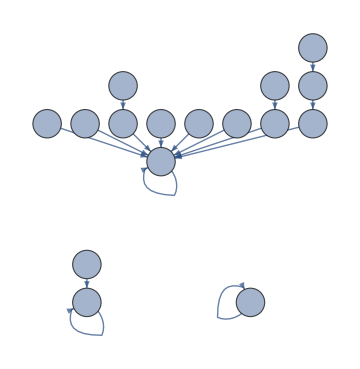

{0.8125,0.0625,0.,0.,0.,0.,0.,0.,0.,0.125,0.,0.,0.,0.,0.,0.}

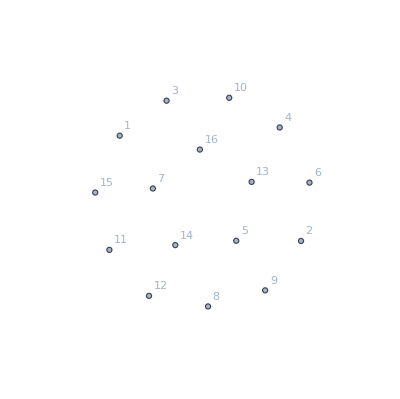

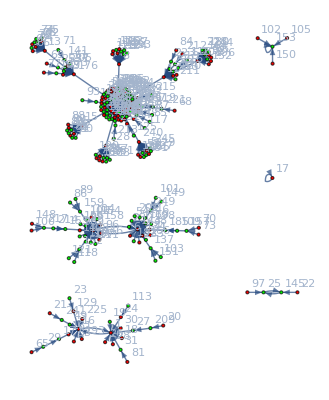

```mathematica
counter[i_,t_,r_,p_,s_,d_]:=
Module[{input = i},
assumptions = {
               If[input[[1]]==0, Q2000>Q2001, Q2000<Q2001],
               If[input[[2]]==0, Q2010>Q2011, Q2010<Q2011],
               If[input[[3]]==0, Q2100>Q2101, Q2100<Q2101],
               If[input[[4]]==0, Q2110>Q2111, Q2110<Q2111]
};
Assuming[assumptions,
{
q1=Simplify[Boole[Q2000>Q2001](p+d*Max[Q1000,Q1001])+Boole[Q2000<Q2001](t+d*Max[Q1010,Q1011])],q2=Simplify[Boole[Q2000>Q2001](s+d*Max[Q1100,Q1101])+Boole[Q2000<Q2001](r+d*Max[Q1110,Q1111])],q3=Simplify[Boole[Q2100>Q2101](p+d*Max[Q1000,Q1001])+Boole[Q2100<Q2101](t+d*Max[Q1010,Q1011])],q4=Simplify[Boole[Q2100>Q2101](s+d*Max[Q1100,Q1101])+Boole[Q2100<Q2101](r+d*Max[Q1110,Q1111])],q5=Simplify[Boole[Q2010>Q2011](p+d*Max[Q1000,Q1001])+Boole[Q2010<Q2011](t+d*Max[Q1010,Q1011])],q6=Simplify[Boole[Q2010>Q2011](s+d*Max[Q1100,Q1101])+Boole[Q2010<Q2011](r+d*Max[Q1110,Q1111])],q7=Simplify[Boole[Q2110>Q2111](p+d*Max[Q1000,Q1001])+Boole[Q2110<Q2111](t+d*Max[Q1010,Q1011])],q8=Simplify[Boole[Q2110>Q2111](s+d*Max[Q1100,Q1101])+Boole[Q2110<Q2111](r+d*Max[Q1110,Q1111])]
}];

sol=Solve[{q1==Q1000, q2==Q1001, q3==Q1010, q4==Q1011, q5==Q1100, q6==Q1101, q7==Q1110, q8==Q1111},
                        {Q1000, Q1001, Q1010, Q1011, Q1100, Q1101, Q1110, Q1111}];
output = {0,0,0,0};
output[[1]]=Boole[sol[[1]][[1]][[2]] < sol[[1]][[2]][[2]]];
output[[2]]=Boole[sol[[1]][[3]][[2]] < sol[[1]][[4]][[2]]];
output[[3]]=Boole[sol[[1]][[5]][[2]] < sol[[1]][[6]][[2]]];
output[[4]]=Boole[sol[[1]][[7]][[2]] < sol[[1]][[8]][[2]]];
output
];

(*All 16 strategies*)
strats = {};
Do[AppendTo[strats, Join[ConstantArray[0,4-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,15}];

(*Calculate the best responses*)
(*Change the values here*)
bestresps = {};
Do[AppendTo[bestresps, counter[strats[[i]],1,7/8,1/4,0,1/2]],{i,1,16}]

(*All 256 strategy pairs*)
inputlist = {};
Do[AppendTo[inputlist, Join[ConstantArray[0,8-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,255}];

(*Find the best responses to the pairs*)
counterstrats = {};
Do[
p1 =FromDigits[inputlist[[i]][[1;;4]],2] + 1 ;
p2 = FromDigits[inputlist[[i]][[5;;8]],2] + 1 ;
AppendTo[counterstrats,Join[bestresps[[p2]],bestresps[[p1]]]];
,{i,1,256}];


(*Make the small graph*)
edges = {};
Do[AppendTo[edges, FromDigits[strats[[i]],2]->FromDigits[bestresps[[i]],2]],{i,1,16}];
Graph[edges, VertexLabels->Placed[Automatic,Center],VertexSize->.75, VertexLabelStyle->20, ImageSize->Medium]

transitionmatrix = AdjacencyMatrix[edges];
P = DiscreteMarkovProcess[ConstantArray[1/16,16],transitionmatrix];
N[PDF[StationaryDistribution[P],Table[i,{i,1,16}]]]

edges = {};
Do[Do[AppendTo[edges,i->j],{j,1,16}],{i,1,16}];
weights = ConstantArray[0,Length[edges]];
Do[Do[If[i==(FromDigits[inputlist[[i]],2] )&& j==(FromDigits[bestresps[[i]],2]),weights[[(i-1)*16+j]]=1,weights[[(i-1)*16+j]]=0],{j,1,16}],{i,1,16}]
Graph[edges,VertexLabels->Automatic,EdgeStyle->Thread[edges->(Opacity[#]&/@weights)],ImageSize->Full]


(*Make the large graph*)
edges = {};
Do[AppendTo[edges, FromDigits[inputlist[[i]],2]->FromDigits[counterstrats[[i]],2]],{i,1,256}]
GraphPlot[edges, VertexLabels->Automatic, DirectedEdges->True, ImageSize->Full, VertexStyle->coloring]
```

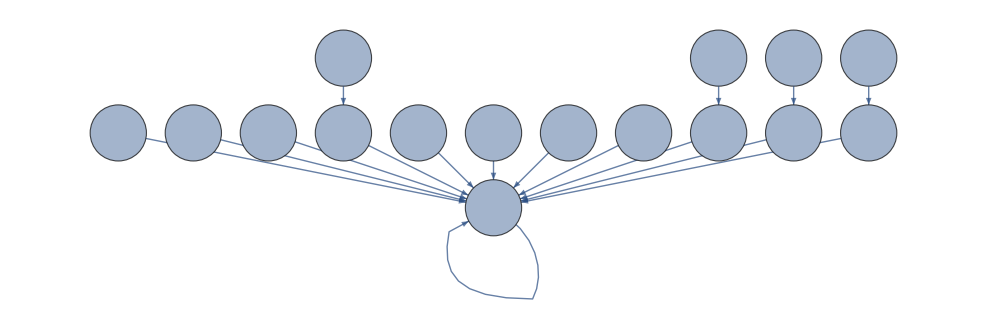

-Graphics-

```mathematica
RegionPlot3D[(s+d s > p+d t&&t + d s > r+d t) /.{t->1,p->0},{r,0,1},{s,0,1},{d,0,1}]
```

-Graphics3D-